# Dielectric polarization processes

This notebook serves as reference source code for the paper, which can be found here:

### utility stuff

```mathematica
Needs["PlotLegends`"];
createLegend[legendLabels_, fontSize_, position_] := Module[{items},
items = Map[Text[Style[#,fontSize]]&,legendLabels];
PlotLegends->Placed[LineLegend[items,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],position]
]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Set::write: Tag ListLinePlot in SyntaxInformation[ListLinePlot] is Protected.

## Dielectric response curves

```mathematica
χ:=((Subscript[ϵ, r1]+Subscript[κ, 1] Subscript[ϵ, r2])(1-I ω Subscript[τ, 2])+(Subscript[ϵ, r2]+Subscript[κ, 2] Subscript[ϵ, r1])(1-I ω Subscript[τ, 1])-Subscript[κ, 2](Subscript[ϵ, r1]+Subscript[κ, 1] Subscript[ϵ, r2])-Subscript[κ, 1](Subscript[ϵ, r2]+Subscript[κ, 2] Subscript[ϵ, r1]))/((1-I ω Subscript[τ, 1])(1-I ω Subscript[τ, 2])-Subscript[κ, 1] Subscript[κ, 2]);

imχ=ComplexExpand[Im[χ]]//Simplify
reχ=ComplexExpand[Re[χ]]//Simplify

ExportString[reχ,"TeX"];
```

(ω (ϵ_r1 τ_1 (1+κ_1 κ_2^2+ω^2 τ_2^2-κ_2 (1+κ_1-ω^2 τ_1 τ_2))+ϵ_r2 τ_2 (1+κ_1^2 κ_2+ω^2 τ_1^2-κ_1 (1+κ_2-ω^2 τ_1 τ_2))))/(κ_1^2 κ_2^2+2 κ_1 κ_2 (-1+ω^2 τ_1 τ_2)+(1+ω^2 τ_1^2) (1+ω^2 τ_2^2))

(ϵ_r1 (1+κ_1^2 κ_2^2+ω^2 τ_2^2+ω^2 κ_2 τ_1 (τ_1+τ_2)+κ_1 κ_2 (-2+ω^2 τ_1 τ_2))+ϵ_r2 (1+κ_1^2 κ_2^2+ω^2 τ_1^2+κ_1 (ω^2 τ_2 (τ_1+τ_2)+κ_2 (-2+ω^2 τ_1 τ_2))))/(κ_1^2 κ_2^2+2 κ_1 κ_2 (-1+ω^2 τ_1 τ_2)+(1+ω^2 τ_1^2) (1+ω^2 τ_2^2))

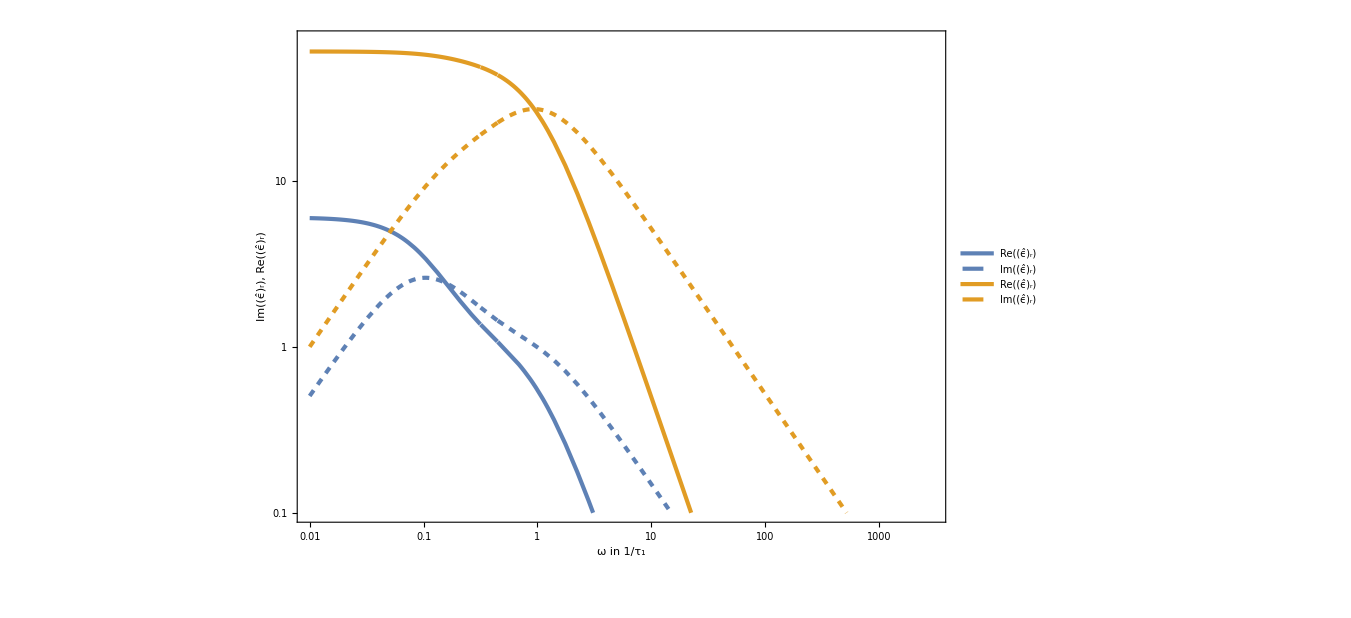

```mathematica
rules1={Subscript[τ, 1]->1,Subscript[τ, 2]->10,Subscript[ϵ, r1]->1,Subscript[ϵ, r2]->5, Subscript[κ, 1]->0.0,Subscript[κ, 2]->0.0};
rules2={Subscript[τ, 1]->1,Subscript[τ, 2]->5,Subscript[ϵ, r1]->50,Subscript[ϵ, r2]->10, Subscript[κ, 1]->0.0,Subscript[κ, 2]->0.0};
imχ=Im@χ /.rules1;
reχ=Re@χ /.rules1;
imχ2=Im@χ /.rules2;
reχ2=Re@χ /.rules2;

labels = {"Re((ϵ̂)_r)", "Im((ϵ̂)_r)", "Re((ϵ̂)_r)", "Im((ϵ̂)_r)"};

dielectricSimplePlot = 
LogLogPlot[{reχ,imχ,reχ2,imχ2} ,{ω,0.01,1000},PlotRange->{{0.01,3000},{0.1,70}},
PlotStyle->{AbsoluteThickness[3],{ColorData[97,"ColorList"]⟦1⟧,Dashed, AbsoluteThickness[3]},{ColorData[97,"ColorList"]⟦2⟧,AbsoluteThickness[3]},{ColorData[97,"ColorList"]⟦2⟧,Dashed, AbsoluteThickness[3]}},
FrameStyle->Directive[Black], Frame->{True,True,False,False},FrameLabel->{"ω in 1/τ_1","Im((ϵ̂)_r), Re((ϵ̂)_r)"},PlotRangePadding -> 0,
FrameTicks->{{0.01,0.1,1,10, 100},{.3,1,3,10,50}},BaseStyle->{FontSize->30},ImageSize->1000, Evaluate@createLegend[labels, 30, {0.85,0.65}] ]
```

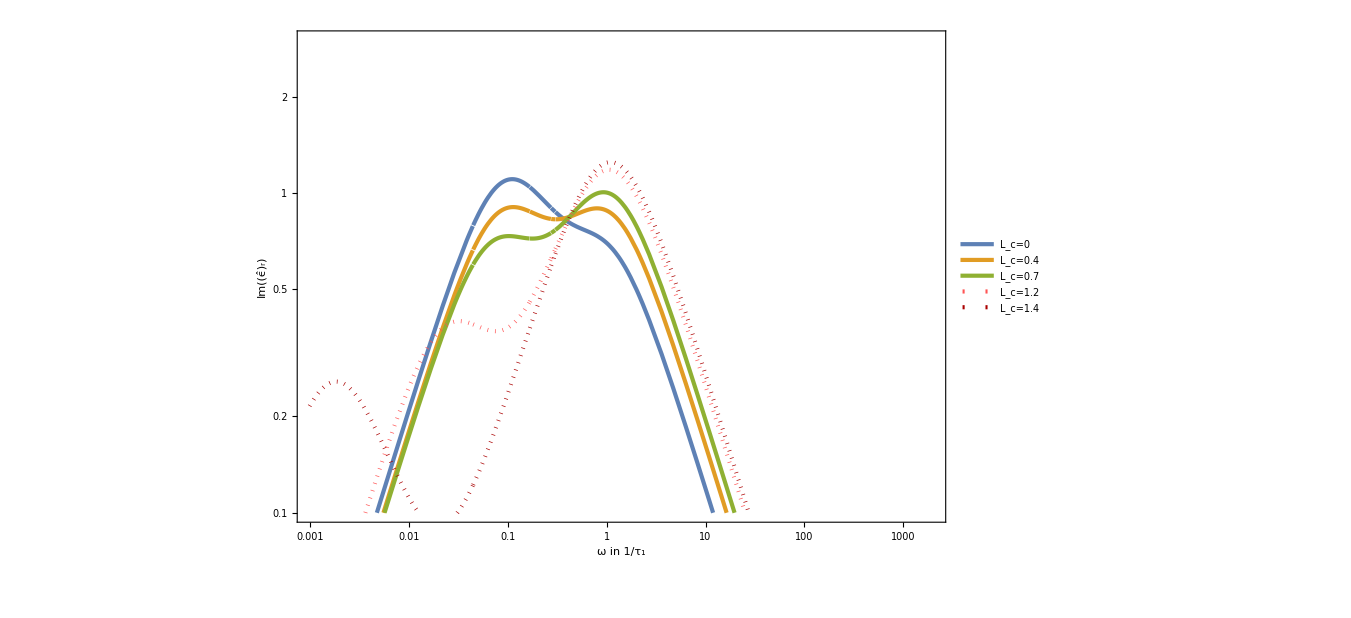

```mathematica
fixedParams = {Subscript[τ, 1]->1,Subscript[τ, 2]->10,Subscript[ϵ, 0]->1,Subscript[ϵ, r1]->1,Subscript[ϵ, r2]->2};
coupling = {Subscript[κ, 1]->Lc/(Subscript[ϵ, r2] Subscript[ϵ, 0]),Subscript[κ, 2]->Lc/(Subscript[ϵ, r1] Subscript[ϵ, 0])};
Lcs={0,0.4,0.7,1.2,1.4};

plotFns=Map[Im@χ /. coupling /.fixedParams /.Lc->#& , Lcs];

labels = Map["L_c="<>ToString@#&,Lcs];

dielectricCouplingPlot = 
LogLogPlot[{plotFns⟦1⟧,plotFns⟦2⟧,plotFns⟦3⟧,plotFns⟦4⟧,plotFns⟦5⟧}, {ω,0.001,1000},
PlotRange->{{0.001,2000},{0.1,3}}, PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Lighter@Red,Dotted,AbsoluteThickness[3]},{Darker@Red,Dotted,AbsoluteThickness[3]}},
FrameStyle->Directive[Black], Frame->{True,True,False,False},FrameLabel->{"ω in 1/τ_1","Im((ϵ̂)_r)"},PlotRangePadding -> 0,
FrameTicks->{{0.01,0.1,1,10,100},{.2,.5,1,2}},BaseStyle->{FontSize->30}, ImageSize->1000, 
Evaluate@createLegend[labels, 30, {0.85,0.5}]
]
```

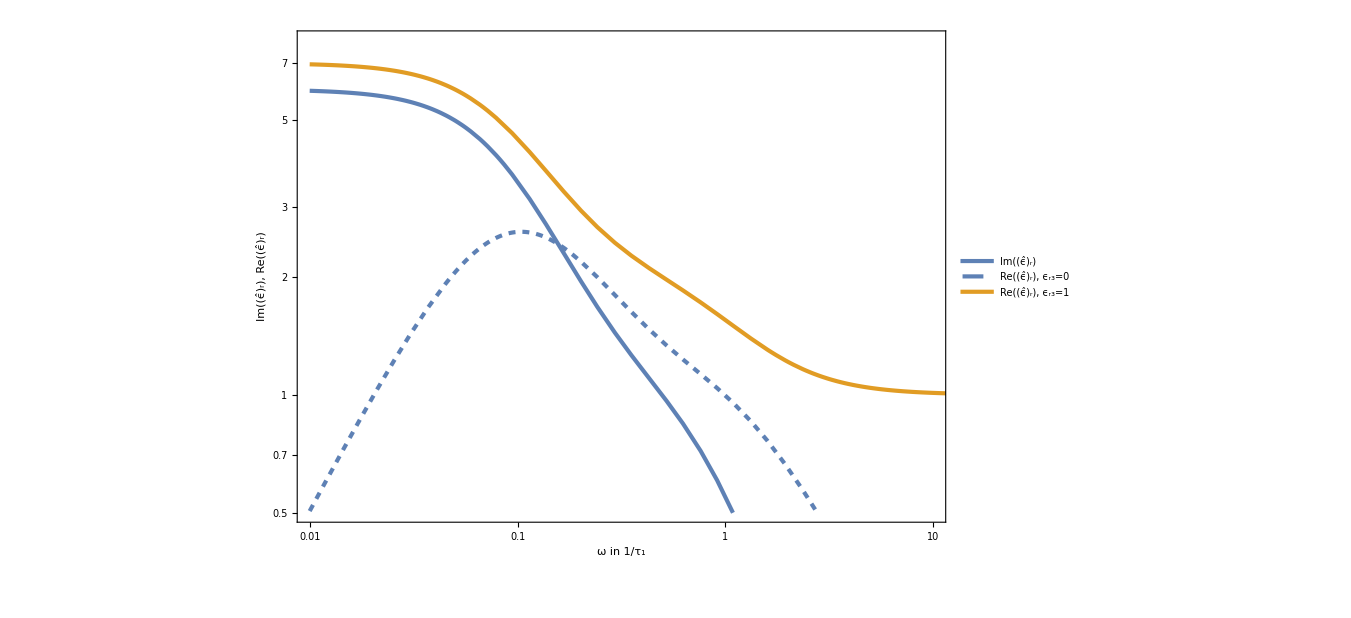

```mathematica
real=Subscript[ϵ, r1]/(1+ ω^2 Subscript[τ, 1]^2)+Subscript[ϵ, r2]/(1+ ω^2 Subscript[τ, 2]^2)+Subscript[ϵ, r3];
plot1=real/.{Subscript[τ, 1]->1,Subscript[τ, 2]->10,Subscript[ϵ, r1]->1,Subscript[ϵ, r2]->5,Subscript[ϵ, r3]->1};
im=(Subscript[ϵ, r1] ω Subscript[τ, 1])/(1+ ω^2 Subscript[τ, 1]^2)+(Subscript[ϵ, r2] ω Subscript[τ, 2])/(1+ ω^2 Subscript[τ, 2]^2);
plot2=im/.{Subscript[τ, 1]->1,Subscript[τ, 2]->10,Subscript[ϵ, r1]->1,Subscript[ϵ, r2]->5};
plot3=real/.{Subscript[τ, 1]->1,Subscript[τ, 2]->10,Subscript[ϵ, r1]->1,Subscript[ϵ, r2]->5,Subscript[ϵ, r3]->0};

labels = {"Im((ϵ̂)_r)", "Re((ϵ̂)_r), ϵ_r3=0", "Re((ϵ̂)_r), ϵ_r3=1"};

dielectricFastPlot =
LogLogPlot[{plot3,plot2,plot1},{ω,0.01,100},
PlotRange->{{0.01,10},{0.5,8}}, PlotStyle->{{AbsoluteThickness[3],ColorData[97,"ColorList"]⟦1⟧},{AbsoluteThickness[3],ColorData[97,"ColorList"]⟦1⟧,Dashed}, {AbsoluteThickness[3],ColorData[97,"ColorList"]⟦2⟧}},
FrameStyle->Directive[Black], Frame->{True,True,False,False}, FrameLabel->{"ω in 1/τ_1","Im((ϵ̂)_r), Re((ϵ̂)_r)"}, PlotRangePadding->0,
FrameTicks->{{0.01,0.1,1,10},{1,2,4,7}},BaseStyle->{FontSize->30}, ImageSize->1000, 
Evaluate@createLegend[labels, 30, {0.8,0.7}]]
```

## High frequency asymptotics

### Analytic solution

Telegrapher’s-Klein-Gordon-equation (TKG):
E^(..)-v.b2 E_xx+2 a Ė+(a.b2-b.b2)E=0

solution (found in “Wave Theory and Applications” by D.R. Bland, page 163-180)
E(x,t) = e^(-ax/v)f(t-x/v)θ(t-x/v) bx/v(∫^t)_(x/v)f(t-u)(e^(-a u)(u.b2-(x.b2)/(v.b2)))^(-1/2)I_2(1,(b(u.b2-(x.b2)/(v.b2)))^(-1/2))du

```mathematica
eqBland[f_,a_,b_,v_,t_,x_]:=
Exp[-((a x)/v)] f[t-x/v] UnitStep[t-x/v]+UnitStep[t-x/v] (b x)/v NIntegrate[f[t-u] Exp[-a u] (u^2-x^2/v^2)^(-(1/2)) BesselI[1,b (u^2-x^2/v^2)^(1/2)],{u,t,x/v}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Plot::exclul: {(u^2-x^2)-0,(-2+x)-0,(2-x)-0,Im[u^2-x^2]-0} must be a list of equalities or real-valued functions.

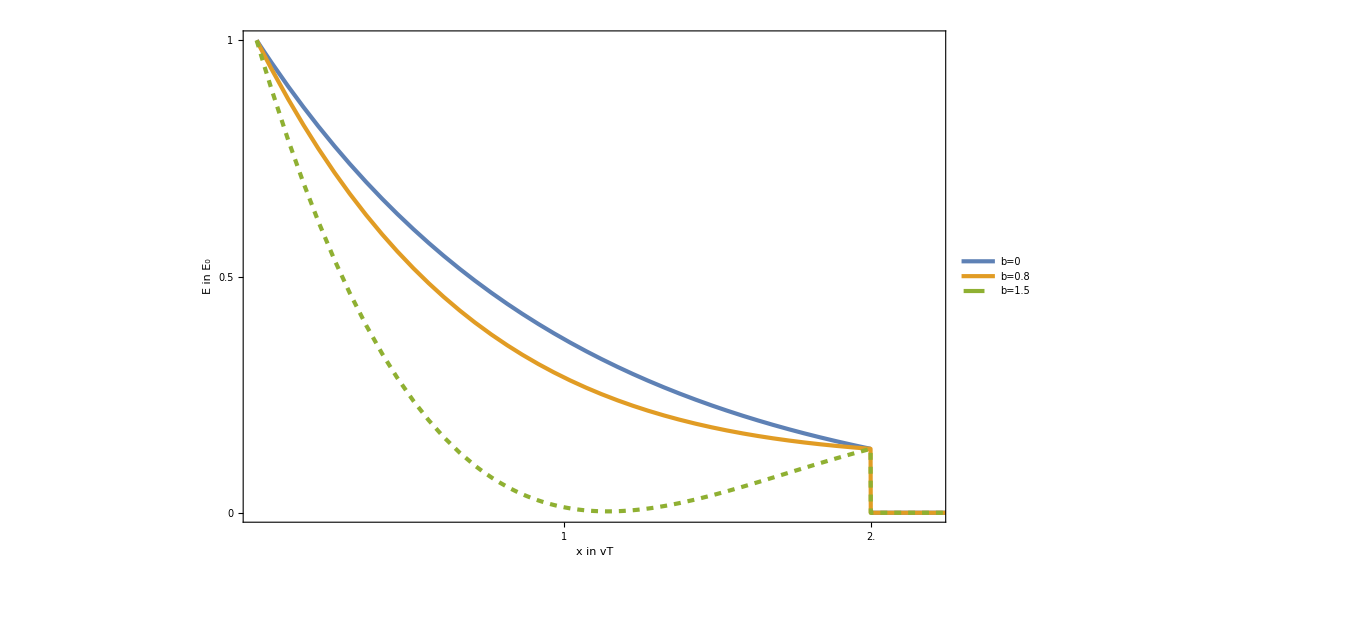

```mathematica
Needs["PlotLegends`"]
bs = {0,0.8,1.5};
labels = Map["b="<>ToString@#&,bs];
bsPlot = Plot[{eqBland[1&,1,bs[[1]],1,2,x],eqBland[1&,1,bs[[2]],1,2,x],eqBland[1&,1,bs[[3]],1,2,x]},{x,0,2.5},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],{AbsoluteThickness[3],Dashed}},AxesLabel->{"x","E"},
PlotRange->{{0,2.2},{0,1}}, FrameStyle->Directive[Black], Frame->{True,True,False,False},FrameLabel->{"x in vT","E in E_0"},PlotRangePadding -> 0,
FrameTicks->{{1,2.0},{0,0.5,1}},BaseStyle->{FontSize->30}, ImageSize->1000, Evaluate@createLegend[labels, 30, {0.8,0.6}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.498104}. NIntegrate obtained -0.153339 and 0.0000440362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.19889}. NIntegrate obtained -0.0859227 and 0.0000348194 for the integral and error estimates.

Plot::exclul: {(u^2-x^2)-0,-Im[x]-0,-x-0,(-1+x)-0,(1-x)-0,Im[u^2-x^2]-0} must be a list of equalities or real-valued functions.

Plot::exclul: {(u^2-x^2)-0,-Im[x]-0,(-1.5+x)-0,(1.5-x)-0,(0.5-x)-0,Im[u^2-x^2]-0} must be a list of equalities or real-valued functions.

Plot::exclul: {(u^2-x^2)-0,-Im[x]-0,(-2.2+x)-0,(2.2-x)-0,(1.2-x)-0,Im[u^2-x^2]-0} must be a list of equalities or real-valued functions.

General::stop: Further output of Plot::exclul will be suppressed during this calculation.

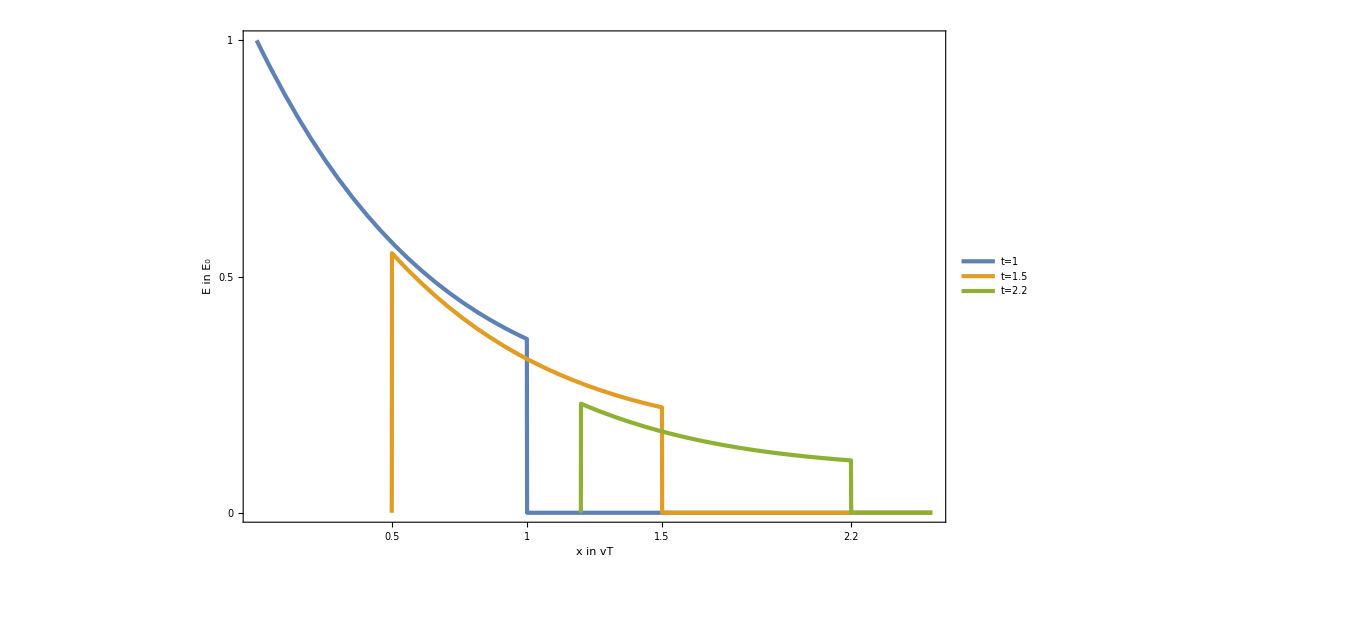

```mathematica
Needs["PlotLegends`"]
einspuls[g_]:=HeavisideTheta[g]-HeavisideTheta[g-1]

ts = {1, 1.5, 2.2};
labels = Map["t="<>ToString@#&,ts];

thetaPulsePlot = Plot[{eqBland[einspuls,1,0.75,1,1,x],eqBland[einspuls,1,0.75,1,1.5,x],eqBland[einspuls,1,0.75,1,2.2,x]},{x,0,2.5},
PlotRange->{{0,2.5},{0,1}},PlotStyle->{AbsoluteThickness[3]},
FrameStyle->Directive[Black], Frame->{True,True,False,False},FrameLabel->{"x in vT","E in E_0"},PlotRangePadding -> 0,
FrameTicks->{{0.5,1,1.5,2.2},{0,0.5,1}},BaseStyle->{FontSize->30},
ImageSize->1000, Evaluate@createLegend[labels, 30, {0.8,0.7}] ]
```

Analytical solution as table of points (created to make use of ListContourPlot):

```mathematica
points=Table[eqBland[E^-#^2&,1,0.1,1,t,x]//N,{x,0,3,0.01},{t,0,3,0.01}];
```

```mathematica
HFAanalyticContour=ListContourPlot[points//Transpose,PlotRange->Full,
Contours->200,ContourStyle->None,ColorFunction->"Rainbow",
FrameStyle->Directive[Black], FrameLabel->{"x in a_2t_g","t in t_g"},FrameTicks->{{{7{0,0},{100,1},{200,2},{300,3}},None},{{{0,0},{100,1},{200,2},{300,3}},None}},
BaseStyle->{FontSize->20},ImageSize->450, Evaluate@createLegend[labels, 16, {0.8,0.7}] ]
```

-Graphics-

### NDSolve

```mathematica
s=Module[{},
duration=3;
a=1;
b=0.1;
v=1;
width=3;

xAxis={
Derivative[0,0][u][0,x]==ⅇ^(-(1000x)^2),
Derivative[1,0][u][0,x]==0
};
tAxis={
Derivative[0,0][u][t,0]==ⅇ^(-(1t)^2),
Derivative[0,1][u][t,0]==0
};
pde=D[u[t,x], t,t]-v^2 D[u[t,x], x,x]+2a D[u[t,x], t]+(a^2-b^2)u[t,x]==0;
eqns=Flatten@Append[Append[tAxis,xAxis],pde];

method = Method->{"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}};

NDSolve[eqns,u,{t,0,duration},{x,-width,width}, WorkingPrecision->30]
]
```

NDSolve::precw: The precision of the differential equation ({{u[t,0]==ⅇ^(-t^2),u^(0,1)[t,0]==0,u[0,x]==ⅇ^(-1000000 x^2),u^(1,0)[0,x]==0,0.99 u[t,x]-u^(0,2)[t,x]+2 u^(1,0)[t,x]+u^(2,0)[t,x]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::eerr: Warning: scaled local spatial error estimate of 926976. at x = -3. in the direction of independent variable t is much greater than the prescribed error tolerance. Grid spacing with 165 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NDSolve::eerr: Warning: scaled local spatial error estimate of 926976. at x = 3. in the direction of independent variable t is much greater than the prescribed error tolerance. Grid spacing with 165 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{u→InterpolatingFunction[{{0, 3.00000000000000000000000000000}, {-3.00000000000000000000000000000, 3.00000000000000000000000000000}}, <>]}}

```mathematica
HFANDSolveContour = 
ContourPlot[Evaluate[First[u[t,x]/.s]],{x,0,width},{t,0,duration},
PlotRange->{-0.5,1},Contours->200,ContourStyle->None,
FrameStyle->Directive[Black], FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}},ColorFunction->"Rainbow",ClippingStyle->{Purple,Red},FrameLabel->{"x in a_2t_g","t in t_g"},BaseStyle->{FontSize->20},
ImageSize->450]
```

-Graphics-

### Method of characteristics

```mathematica
evaluateMatrixHFA[EtAxisFn_]:=Module[{a,b,v,dt,width,tAxis,ϕFn,first,last,rows,lines},
a=1;
b=0.1;
v=1;(*this is fixed to 1 through hard-coding*)
dt=0.01;
width=3;

ϕFn=D[EtAxisFn,t];
tAxis=Table[{EtAxisFn,0},{t,0,2width,dt}];
tAxis⟦1,2⟧=a tAxis⟦1,1⟧;

evaluatePointOnHeadCharacteristic[lowerLeftPoint_]:=({Subscript[E, c],Subscript[ϕ, c]}/.Solve[(Subscript[E, c]-lowerLeftPoint⟦1⟧)/(1/2dt)- Subscript[ϕ, c]==0&&a Subscript[E, c]+ Subscript[ϕ, c]==0 ,{Subscript[E, c],Subscript[ϕ, c]}])[[1]]; 
evaluatePointOnCharacteristic[lowerLeftPoint_, lowerRightPoint_]:=({Subscript[E, c],Subscript[ϕ, c]}/.Solve[(Subscript[E, c]-lowerLeftPoint⟦1⟧)/(1/2dt)- Subscript[ϕ, c]==0&&(Subscript[E, c]-lowerRightPoint⟦1⟧)/(1/2dt)+ (Subscript[ϕ, c]-lowerRightPoint⟦2⟧)/(1/2dt)+ Subscript[ϕ, c]+(a^2-b^2)/a^2 Subscript[E, c]==0,{Subscript[E, c],Subscript[ϕ, c]}])[[1]];

evaluateLine[lastCharacteristic_]:=Module[{lastPoint,line},
lineNumber++;
lastPoint=tAxis⟦lineNumber⟧;
line=Table[lastPoint=evaluatePointOnCharacteristic[lastPoint,lastCharacteristic⟦n+1⟧ ], {n,1,2*width/dt-lineNumber}];
Prepend[line,tAxis⟦lineNumber⟧]
];

lineNumber=1;
lastPoint=tAxis⟦lineNumber⟧;
headCharacteristic=Table[lastPoint=evaluatePointOnHeadCharacteristic[lastPoint], {n,1,2*width/dt}];
headCharacteristic=Prepend[headCharacteristic,tAxis⟦lineNumber⟧];

first=evaluateLine[headCharacteristic];

last=first;
lines=Table[last=evaluateLine[last],{n,1,width/dt}];
lines=Prepend[lines,first];
lines=Prepend[lines,headCharacteristic];

(* Length@result
Map[Length, result]*)

rows = Floor[width/dt];
Table[
PadRight[Table[lines⟦row-n,2n+1,1⟧, {n,0,row-1}],rows],
{row,1,rows}]
]
```

```mathematica
resultHFA=evaluateMatrixHFA[ⅇ^(-(t)^2)];
```

```mathematica
HFAnumericContour=ListContourPlot[resultHFA,
PlotRange->Full,Contours->200,ContourStyle->None,ColorFunction->"Rainbow",
FrameStyle->Directive[Black], FrameLabel->{"x in a_2t_g","t in t_g"}, FrameTicks->{{{{0,0},{100,1},{200,2},{300,3}},None},{{{0,0},{100,1},{200,2},{300,3}},None}}, BaseStyle->{FontSize->20},
ImageSize->450]
```

-Graphics-

## Full relaxation equation (no asymptotics)

```mathematica
(* 2 polarization processes *)
EvaluateMatrix2P[EtAxisFn_,τ1_,ϵr1_,τ2_,ϵr2_]:=Module[{v,dt,tAxis,first,last,rows,lines, lineNumber, headCharacteristic},
v=1;(*this is fixed to 1 through hard-coding*)

dt=0.01;
width=5;

(* evaluation functions *)

jumpEquation:=Subscript[E, c]== v Subscript[B, c] ;
(* positive characteristic equation, x = v t + const *)
posCharEq[lowerPoint_]:=(Subscript[E, c]-lowerPoint⟦1⟧)/(1/2dt)+ ϵr1/τ1 Subscript[E, c]+ϵr2/τ2 Subscript[E, c]+v(Subscript[B, c]-lowerPoint⟦2⟧)/(1/2dt)-π1c/τ1-π2c/τ2==0;
(* negative characteristic equation, x = v t + const *)
negCharEq[lowerPoint_]:=(Subscript[E, c]-lowerPoint⟦1⟧)/(1/2dt)+ ϵr1/τ1 Subscript[E, c]+ ϵr2/τ2 Subscript[E, c]-v(Subscript[B, c]-lowerPoint⟦2⟧)/(1/2dt)-π1c/τ1-π2c/τ2==0;
(* relaxation equation, x = const *)
relaxEq1[lowerPoint_]:=(π1c-lowerPoint⟦3⟧)/dt+π1c/τ1-ϵr1/τ1 Subscript[E, c]==0;
relaxEq2[lowerPoint_]:=(π2c-lowerPoint⟦3⟧)/dt+π2c/τ2-ϵr2/τ2 Subscript[E, c]==0;

evaluatePointOnHeadCharacteristic[lowerLeftPoint_]:=({Subscript[E, c],Subscript[B, c],0,0}/.Solve[(Subscript[E, c]-lowerLeftPoint⟦1⟧)/(1/2dt)+ϵr1/τ1 Subscript[E, c]+ϵr2/τ2 Subscript[E, c]+v(Subscript[B, c]-lowerLeftPoint⟦2⟧)/(1/2dt)==0&&jumpEquation ,{Subscript[E, c],Subscript[B, c]}])⟦1⟧;

evaluatePointOnCharacteristic[lowerLeftPoint_, lowerRightPoint_, lowerPoint_]:=({Subscript[E, c],Subscript[B, c],π1c, π2c}/.Solve[posCharEq[lowerLeftPoint]&&negCharEq[lowerRightPoint]&&relaxEq1[lowerPoint]&&relaxEq2[lowerPoint],{Subscript[E, c],Subscript[B, c],π1c,π2c}])⟦1⟧;

evaluateNextCharacteristic[lastCharacteristic_]:=Module[{lastPoint,line, const},
lineNumber++;

(* evaluate the correct B on t Axis *)
tAxis⟦lineNumber,2⟧=Subscript[B, c]/.Solve[negCharEq[lastCharacteristic⟦2⟧]/.{πc->tAxis⟦lineNumber,3⟧,Subscript[E, c]->tAxis⟦lineNumber,1⟧},Subscript[B, c]];

lastPoint=tAxis⟦lineNumber⟧;
line=Table[lastPoint=evaluatePointOnCharacteristic[lastPoint,lastCharacteristic⟦n+2⟧,lastCharacteristic⟦n+1⟧], {n,1,2width/dt-lineNumber}];
Prepend[line,tAxis⟦lineNumber⟧]
];

(* begin of evaluation *)
first={EtAxisFn/.t->0,EtAxisFn/.t->0,0,0};
last=first;
tAxis=Table[last={EtAxisFn,0, (π1c/.Solve[relaxEq1[last]/.Subscript[E, c]->EtAxisFn,π1c])⟦1⟧,(π2c/.Solve[relaxEq2[last]/.Subscript[E, c]->EtAxisFn,π2c])⟦1⟧},{t,dt,2width,dt}];
tAxis=Prepend[tAxis,first];


lineNumber=1;
last=tAxis⟦lineNumber⟧;
headCharacteristic=Table[last=evaluatePointOnHeadCharacteristic[last], {n,1,2width/dt}];
headCharacteristic=Prepend[headCharacteristic,tAxis⟦lineNumber⟧];

first=evaluateNextCharacteristic[headCharacteristic];

last=first;
lines=Table[last=evaluateNextCharacteristic[last],{n,1,width/dt}];
lines=Prepend[lines,first];
lines=Prepend[lines,headCharacteristic];

rows = Floor[width/dt];
Table[
PadRight[Table[lines⟦row-n,2n+1,1⟧, {n,0,row-1}],rows],
{row,1,rows}]
]
```

```mathematica
fullResult1=EvaluateMatrix2P[E^(-(1 t)^2),0.1,0.1,0.2,0.2];
fullResult2=EvaluateMatrix2P[E^(-(1 t)^2),1,10,100,20];
```

```mathematica
fullEqFastContour=ListContourPlot[fullResult1,PlotRange->Full,
Contours->200,ColorFunction->"Rainbow",ContourStyle->None,
FrameStyle->Directive[Black], FrameLabel->{"x in a_2t_g","t in t_g"},FrameTicks->{{{{0,0},{Length@fullResult1/width*2.5,2.5},{Length@fullResult1/width*5,5}},None},{{{0,0},{Length@fullResult1/width*2.5,2.5},{Length@fullResult1/width*5,5}},None}},
BaseStyle->{FontSize->20},ImageSize->450]
```

-Graphics-

```mathematica
fullEqSlowContour=ListContourPlot[fullResult2,PlotRange->Full,
ColorFunction->"Rainbow",Contours->200,ContourStyle->None,
FrameStyle->Directive[Black], FrameLabel->{"x in a_2t_g","t in t_g"},FrameTicks->{{{{0,0},{Length@fullResult1/width*2.5,2.5},{Length@fullResult1/width*5,5}},None},{{{0,0},{Length@fullResult1/width*2.5,2.5},{Length@fullResult1/width*5,5}},None}},
BaseStyle->{FontSize->20},ImageSize->450]
```

-Graphics-

```mathematica
Join[ts,ts]
```

{1,1.5,2.2,1,1.5,2.2}

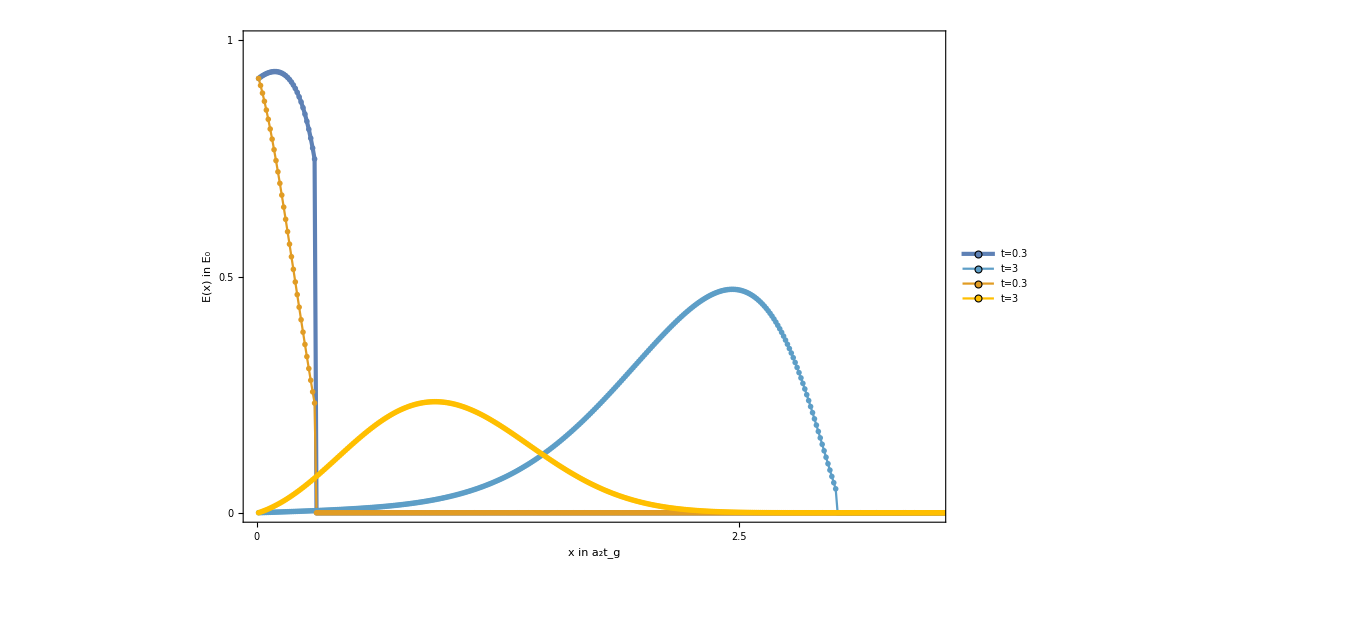

```mathematica
Module[{ts},
width = 5;
ts = {0.3, 3};
cutline1 = Length@fullResult1/width*ts⟦1⟧;
cutline2 = Length@fullResult1/width*ts⟦2⟧;

fullCutlinePlot=ListPlot[{fullResult1[[cutline1]], fullResult1[[cutline2]], fullResult2[[cutline1]],fullResult2[[cutline2]]}, 
PlotRange->{{0,Length@fullResult1/width*3.5},{0,1}},PlotMarkers->{{Graphics[{Disk[]}], 1/70}, {Graphics[{Disk[]}], 1/70}},Joined->True,
PlotStyle->{{AbsoluteThickness[3],ColorData[97,"ColorList"]⟦1⟧}, {AbsoluteThickness[3],ColorData[97,"ColorList"]⟦7⟧}, {AbsoluteThickness[3],ColorData[97,"ColorList"]⟦2⟧}, {AbsoluteThickness[3],ColorData[97,"ColorList"]⟦8⟧}},
Frame->{True,True,False,False},FrameLabel->{"x in a_2t_g","E(x) in E_0"}, PlotRangePadding -> 0,
FrameStyle->Directive[Black], FrameTicks->{{{0,0},{Length@fullResult1/width*2.5,2.5},{Length@fullResult1/5*5,5},{Length@fullResult1/5*15,15}},{1,0.5,0}},BaseStyle->{FontSize->30},
ImageSize->1000, Evaluate@createLegend[Map["t="<>ToString@#&,Join[ts,ts]], 30, {0.9,0.7}]]
]
```

## Visualizations and Export

#### visualizations

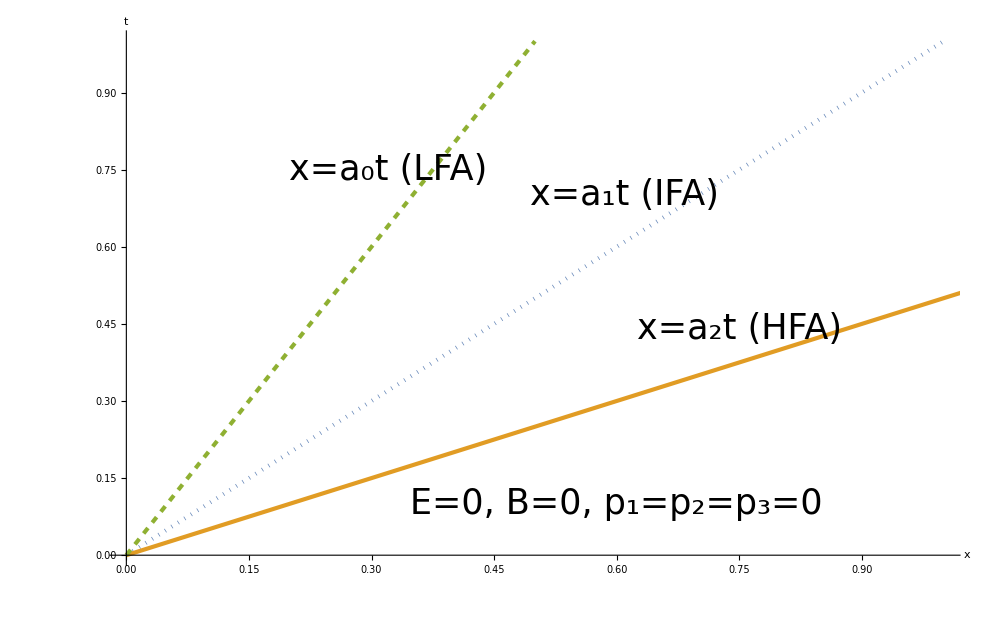

```mathematica
a=Plot[{x, 1/2 x, 2 x}, {x, 0, 10}, PlotRange -> {{0, 1}, {0, 1}}, PlotStyle->{{Automatic,Dotted,AbsoluteThickness[3]}, {Automatic,AbsoluteThickness[3]}, {Automatic, Dashed,AbsoluteThickness[3]}},
PlotStyle -> AbsoluteThickness[4], Ticks->None, BaseStyle->{Black, FontSize->45},
AxesLabel -> {"x", "t"}, AxesStyle->{{Directive[Black],Thickness[0.005],Arrowheads[{0.0, 0.025}]},{Directive[Black],Thickness[0.005],Arrowheads[{0.0, 0.025}]}},
ImageSize -> 1000];
hfa = Graphics[Rotate[Text[Style["x=a_2t (HFA)", FontSize ->35], {0.75, 0.44}], 30 Degree]];
ifa = Graphics[Rotate[Text[Style["x=a_1t (IFA)", FontSize ->35], {0.61, 0.7}], 45 Degree]];
lfa = Graphics[Rotate[Text[Style["x=a_0t (LFA)", FontSize ->35], {0.32, 0.75}], 65 Degree]];
ff = Graphics[Rotate[Text[Style["E=0, B=0, p_1=p_2=p_3=0", FontSize ->35], {0.6, 0.1}], 0 Degree]];
LFAIFAHFAPlot = Show[a, ifa, lfa, hfa, ff, ImageSize -> 1000]
```

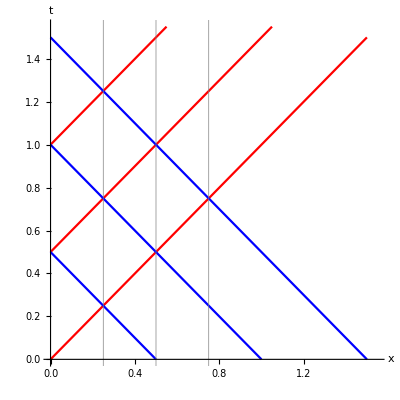

```mathematica
characteristicsPlot=Plot[{x, x + 0.5, x + 1, 1 - x, 0.5 - x, 1.5 - x}, {x, 0, 1.5}, 
   PlotRange -> {{0, 1.55}, {0, 1.55}}, PlotStyle -> {{Red}, {Red}, {Red}, {Blue}, {Blue}, {Blue}}, 
   AspectRatio -> Automatic, AxesStyle->Directive[Black],
   GridLines -> {{{0.25, Gray}, {0.5, Gray}, {0.75, Gray}}, None}, GridLinesStyle->Directive[Thick, Gray], Ticks -> None, 
  AxesLabel -> {"x","t"} , AxesStyle -> Arrowheads[{0.0, 0.025}], BaseStyle->{FontSize->30}]
```

#### export of images

```mathematica
dir="/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/";
exportIt=Export[dir<>#[[2]]<>".png",#[[1]]]&;
```

```mathematica
plots = {dielectricCouplingPlot,dielectricSimplePlot,dielectricFastPlot,thetaPulsePlot,bsPlot,fullCutlinePlot,LFAIFAHFAPlot,characteristicsPlot};
plotnames = {"dielectric-coupling","dielectric-simple","dielectric-fast","theta-pulse","bs","full-eq-cutlines","LFA-IFA-HFA-plot","characteristics"};
zipped=MapThread[{#1,#2}&,{plots,plotnames}];
exportIt /@ zipped
```

{/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/dielectric-coupling.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/dielectric-simple.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/dielectric-fast.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/theta-pulse.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/bs.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/full-eq-cutlines.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/LFA-IFA-HFA-plot.png,/mnt/4TBintern/SharedShitzens/Physik/Latex/Paper/LKIT/pics/characteristics.png}

```mathematica
addlegend=ShowLegend[#,{ColorData["Rainbow"][1 - #1] &, 10, 
  "\n\n\n\n\n\n E_0 \n\n E(x,t)= \n\n 1/2 E_0 \n\n 1/4 E_0","   0", LegendPosition -> {0.5, -.6}, LegendSize->{0.5, 1},
  BaseStyle -> {FontSize -> 13}}]&;

plots=addlegend /@ {HFAnumericContour, HFAanalyticContour, HFANDSolveContour, fullEqSlowContour, fullEqFastContour};
plotnames={"HFA-numeric","HFA-analytic-plot","HFA-NDSolve","full-equation-numeric","full-equation-numeric2"};

zipped=MapThread[{#1,#2}&,{plots,plotnames}];
exportIt/@zipped
```

Export::nodir: Directory /mnt/wwn-0x16268020091034030080x-part1/SharedShitzens/Physik/Latex/Paper/LKIT/pics/ does not exist.

Export::noopen: Cannot open /mnt/wwn-0x16268020091034030080x-part1/SharedShitzens/Physik/Latex/Paper/LKIT/pics/HFA-numeric.png.

Export::nodir: Directory /mnt/wwn-0x16268020091034030080x-part1/SharedShitzens/Physik/Latex/Paper/LKIT/pics/ does not exist.

Export::noopen: Cannot open /mnt/wwn-0x16268020091034030080x-part1/SharedShitzens/Physik/Latex/Paper/LKIT/pics/HFA-analytic-plot.png.

Export::nodir: Directory /mnt/wwn-0x16268020091034030080x-part1/SharedShitzens/Physik/Latex/Paper/LKIT/pics/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

Export::noopen: Cannot open /mnt/wwn-0x16268020091034030080x-part1/SharedShitzens/Physik/Latex/Paper/LKIT/pics/HFA-NDSolve.png.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed}